```mathematica
Clear["Global`*"];
roadRawData=Import[NotebookDirectory[]<>"road.json"];
roadData=({#⟦2⟧⟦2⟧⟦1⟧⟦2⟧,#⟦3⟧⟦2⟧⟦2⟧⟦2⟧})&/@roadRawData⟦1⟧⟦2⟧;
```

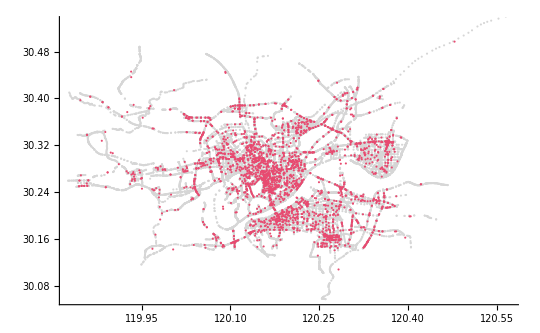

```mathematica
roadDataToPlot=roadData⟦All,2⟧;
ListPlot[{roadDataToPlot~Flatten~1,Mean/@roadDataToPlot},PlotStyle->{GrayLevel[0.84],RGBColor[0.91,0.29,0.44]}]
```

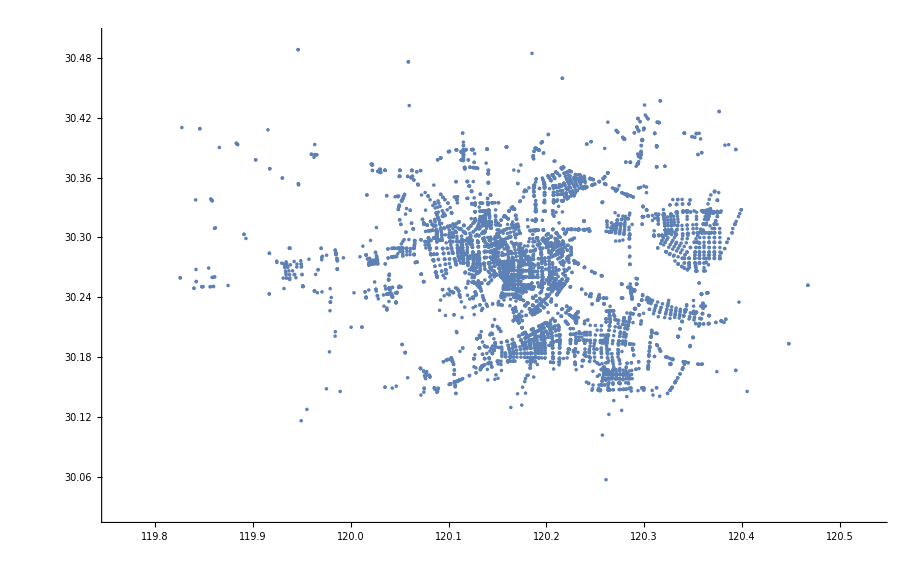

```mathematica
nodeRawData = Import[NotebookDirectory[]<>"nodes.json"];
nodeData=({#⟦2⟧⟦2⟧⟦1⟧⟦2⟧,#⟦3⟧⟦2⟧⟦2⟧⟦2⟧})&/@nodeRawData⟦1⟧⟦2⟧;
nodeDataToPlot=nodeData⟦All,2⟧;
ListPlot[nodeDataToPlot]
```

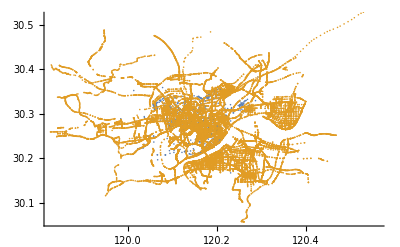

```mathematica
poiRawData = Import[NotebookDirectory[]<>"poi.json"];
poiData=({#⟦2⟧⟦2⟧⟦1⟧⟦2⟧,#⟦3⟧⟦2⟧⟦2⟧⟦2⟧})&/@poiRawData⟦1⟧⟦2⟧;
poiDataToPlot=poiData⟦All,2⟧;
ListPlot[{poiDataToPlot,roadDataToPlot~Flatten~1}]
```

```mathematica
trafficRawData = Import[NotebookDirectory[] <> "hz_stat_50.csv"];
```

```mathematica
takeWeekdayData[data_List, num_]:=Drop[Select[data, #⟦3⟧==num&], None, {3}];
generateListByHour[data_List]:=Table[Drop[Select[data, #⟦2⟧==i&], None, {2}], {i, 0, 23}];
sundayData=generateListByHour@takeWeekdayData[trafficRawData, 0];
mondayData=generateListByHour@takeWeekdayData[trafficRawData, 1];
tuesdayData=generateListByHour@takeWeekdayData[trafficRawData, 2];
wednesdayData=generateListByHour@takeWeekdayData[trafficRawData, 3];
thursdayData=generateListByHour@takeWeekdayData[trafficRawData, 4];
fridayData=generateListByHour@takeWeekdayData[trafficRawData, 5];
saturdayData=generateListByHour@takeWeekdayData[trafficRawData, 6];
```

```mathematica
trafficDataSequence=Join[sundayData,mondayData,tuesdayData,wednesdayData,thursdayData,fridayData,saturdayData];
```

```mathematica
trafficDataSequence⟦1⟧
```

{{2,17,46.1765,2,0.632825},{3,19,43.51,2,0.632804},{5,3,87.66,2,2.50398},{6,7,95.3857,5,6.29326},{9,2111,53.5045,287,13.8074},2346,{2824,88,33.5266,8,3.60449},{2825,2,44.52,2,0.76212},{2826,2,27.205,2,0.761034},{2828,44,49.3843,9,4.0731}}
 |  |  |  |

```mathematica
roadNodeAssoc=Association@@Apply[Rule,roadData,{1}];
avgSpeedDataSequence=Table[Flatten[Transpose[{roadNodeAssoc[#⟦1⟧],Table[#⟦2⟧,roadNodeAssoc[#⟦1⟧]]}]&/@trafficDataSequence⟦i⟧⟦All,{1,3}⟧,1],{i,1,Length@trafficDataSequence}];
densityDataSequence=Table[Flatten[Transpose[{roadNodeAssoc[#⟦1⟧],Table[#⟦2⟧,roadNodeAssoc[#⟦1⟧]]}]&/@trafficDataSequence⟦i⟧⟦All,{1,5}⟧,1],{i,1,Length@trafficDataSequence}];
```

```mathematica
maxT2=Max[densityDataSequence⟦1⟧⟦All,2⟧]
```

93247.7

```mathematica
Export[NotebookDirectory[]<>"data_by_time.json",{{"RoadID","RecordNum","AveSpeed","CarNum","NumPerkm"}}~Join~trafficDataSequence]
```

D:\development\traffic-data\data_by_time.json